## Příklad Ia

◀     |     ▶

1) Zadefinujte funkci f takovou, že f(x)=sinh(x^2) a vytiskněte graf této funkce v argumentu x=√(t+1) pro -1≤t≤1, (libovolně) popište osy a křivka nechť je silná a červená.

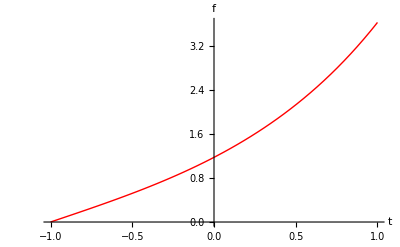

```mathematica
f[x_]:=Sinh[x^2];
Plot[
f[Sqrt[t+1]],
{t,-1,1},
AxesLabel->{"t","f"},
PlotStyle->{Thick,Red}
]
```

2) Vyřešte soustavu rovnic, výsledek dosaďte do výrazu vyr.  Hodnotu výrazu vyr po dosazení zobrazte jako desetinné číslo.

```mathematica
uloha={
b+2 c+a==3,
5 a-3 b+2 c==-4,
-21 a+15 c==3
};
vyr=√a+b^2+c^2;
reseni=Solve[
uloha,
{a,b,c}
];
reseni
(*gives the first element inexpr.*)
N[vyr /.First[reseni]]
```

{{a→17/96,b→185/96,c→43/96}}

4.33509

3) Vyřešte soustavu difrovnic pro soustavu počátečních podmínek, pro 0≤t≤40; vytiskněte graf f[t] a g[t] a pomocí příkazu ParametricPlot také vytiskněte graf  f[t], g[t], tj. graf s funkcí f[t] na vodorovné ose a g[t] na svislé ose.

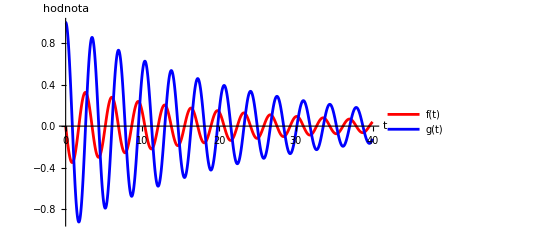

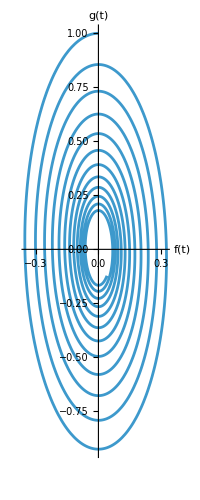

```mathematica
Clear[f,g,t]
soustavaRovnic={
3f'[t]+2g[t]==-E/10*f[t],
5f[t]-g'[t]==0
};
soustavaPodminek={
f[0]==0,
g[0]==1
};
reseni=First[NDSolve[Join[soustavaRovnic,soustavaPodminek],
{f,g},{t,0,40}
]];
Plot[
Evaluate[{f[t],g[t]}/.reseni],
{t,0,40},
PlotStyle->{Red,Blue},
PlotLegends->{"f(t)","g(t)"},
AxesLabel->{"t","hodnota"}
]

ParametricPlot[
Evaluate[{f[t],g[t]}/.reseni],
{t,0,40},
AxesLabel->{"f(t)","g(t)"}
]
```

## Příklad Ib

◀     |     ▶

1) Zadefinujte funkci y takovou, že y(x)=cosh(x^2) a vytiskněte graf této funkce v argumentu x=√(t+2) pro 0≤t≤2, (libovolně) popište osy a křivka nechť je silná a modrá.

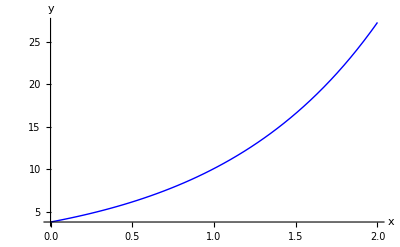

```mathematica
y[x_]:=Cosh[x^2];
Plot[
y[Sqrt[t+2]],
{t,0,2},
AxesLabel->{"x", "y"},
PlotStyle->{Thick, Blue}
]
```

2) Vyřešte soustavu rovnic, výsledek dosaďte do výrazu vyr.  Hodnotu výrazu vyr po dosazení zobrazte jako desetinné číslo.

```mathematica
uloha={
-b+3a==3,
-6 a+17 b+2 c==14,
-21 a+15 c==3
};
vyr=a+b-c;
reseni = Solve[uloha, {a,b,c}];
N[vyr /.First[reseni]]
```

0.313808

3) Vyřešte soustavu difrovnic pro soustavu počátečních podmínek, pro 0≤t≤50; vytiskněte graf x1[t] a x2[t] a pomocí příkazu ParametricPlot také vytiskněte graf  x1[t], x2[t], tj. graf s funkcí x1[t] na vodorovné ose a x2[t] na svislé ose.

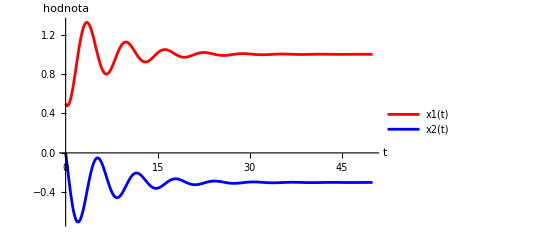

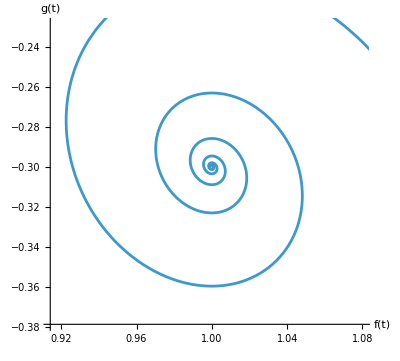

```mathematica
soustavaRovnic={
x1'[t]+x2[t]==-3/10*x1[t],
x1[t]-x2'[t]==1
};
soustavaPodminek={
x1[0]==1/2,
x2[0]==0
};
reseni=First[NDSolve[Join[soustavaRovnic,soustavaPodminek],
{x1,x2},{t,0,50}
]];
Plot[
Evaluate[{x1[t],x2[t]}/.reseni],
{t,0,50},
PlotStyle->{Red,Blue},
PlotLegends->{"x1(t)","x2(t)"},
AxesLabel->{"t","hodnota"}
]
ParametricPlot[
Evaluate[{x1[t],x2[t]}/.reseni],
{t,0,50},
AxesLabel->{"x1(t)","x1(t)"}
]
```

## Příklad Ic

◀     |     ▶

1) Zadefinujte funkci f takovou, že f(x)=cos(x^(3/2)) a vytiskněte graf této funkce v argumentu x=(ln[t])^2 pro 1≤t≤5, (libovolně) popište osy a křivka nechť je zelená.

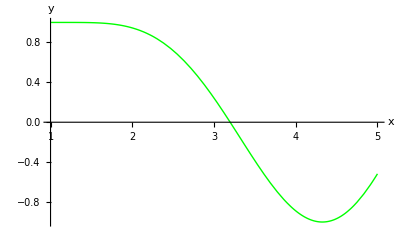

```mathematica
f[x_]:=Cos[x^(3/2)];
Plot[
f[(Log[t])^2],
{t,1,5},
AxesLabel->{"x", "y"},
PlotStyle->{Thick, Green}
]
```

2) Vyřešte soustavu rovnic, výsledek dosaďte do výrazu vyr.  Hodnotu výrazu vyr po dosazení zobrazte jako desetinné číslo.

```mathematica
soustava={
-15x+6z==0,
8.2x+7y-3z==-9,
8x-2y+z==1
};
vyr=2 x^3+3y-6 z^2;
reseni = Solve[soustava, {x,y,z}];
N[vyr /.First[reseni]]
```

-4.62824

3) Vyřešte soustavu difrovnic pro soustavu počátečních podmínek, pro 0≤t≤5; vytiskněte graf x1[t] a x2[t] a pomocí příkazu ParametricPlot také vytiskněte graf  x1[t], x2[t], tj. graf s funkcí x1[t] na vodorovné ose a x2[t] na svislé ose.

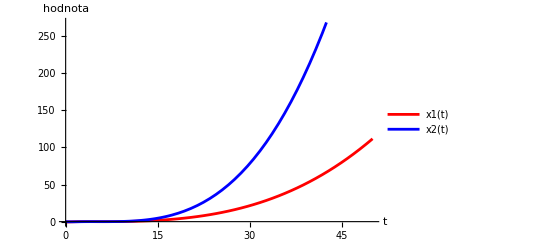

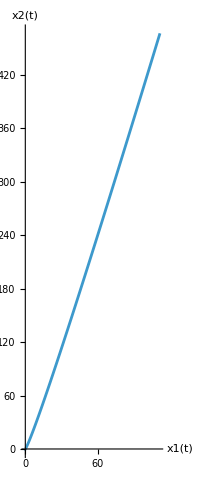

```mathematica
soustavaRovnic={
x1'[t]+x2[t]==-3/10*x1[t],x1[t]-x2'[t]==1*x2[t]
};
soustavaPodminek={
x1[0]==-1/2,
x2[0]==0
};
reseni=First[NDSolve[Join[soustavaRovnic,soustavaPodminek],
{x1,x2},{t,0,5}
]];
Plot[
Evaluate[{x1[t],x2[t]}/.reseni],
{t,0,50},
PlotStyle->{Red,Blue},
PlotLegends->{"x1(t)","x2(t)"},
AxesLabel->{"t","hodnota"}
]
ParametricPlot[
Evaluate[{x1[t],x2[t]}/.reseni],
{t,0,50},
AxesLabel->{"x1(t)","x2(t)"}
]
```

## Příklad Id

◀     |     ▶

1) Zadefinujte funkci y takovou, že y(x)=arctg(x^(3/2)) a vytiskněte graf této funkce v argumentu x=cosh(t) pro -5≤t≤5, (libovolně) popište osy a křivka nechť je žlutá.

2) Vyřešte soustavu rovnic, výsledek dosaďte do výrazu vyr.  Hodnotu výrazu vyr po dosazení zobrazte jako desetinné číslo.

```mathematica
soustava={-15x+3y==0,8x+5y-10z==10,5x-y+z==1};
vyr=√x+2y-6 z^2;
```

3) Vyřešte soustavu difrovnic pro soustavu počátečních podmínek, pro 0≤t≤50; vytiskněte graf f[t] a g[t] a pomocí příkazu ParametricPlot také vytiskněte graf  f[t], g[t], tj. graf s funkcí f[t] na vodorovné ose a g[t] na svislé ose.

```mathematica
soustavaRovnic={f'[t]+g[t]==-1/2*f[t],f[t]-g'[t]==1};
soustavaPodminek={f[0]==0,g[0]==1};
```